## Utility

```mathematica
colorrules =  {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]};
```

```mathematica
getca[ru_, steps_:200, width_:All, init_:{{1}, 0}]:= CellularAutomaton[ru, init, {steps, width}]
```

```mathematica
getca[ru_, {steps_:200, width_:All}, init_:{{1}, 0}]:= CellularAutomaton[ru, init, {steps, width}]
```

```mathematica
TestLifetime[rule_, steps_Integer:200, init_List:{{1}, 0}]:=With[
{array=getca[rule, steps, All, init]},If[#==0,-Infinity,steps-#+1]&[
LengthWhile[Reverse[array],Total[#]==0&]
]
]
```

```mathematica
TestCALifeTime[{ca_List, perturbation_List}]:= TestCALifeTime[ca]
```

```mathematica
TestCALifeTime[ca_List]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]
```

## Visualizations

```mathematica
gettrimoffsets[ca_, {trimwidth_, trimheight_}]:= Module[{left, right, bottom},
{left, right} = Replace[{Flatten[bodyidxs[ca], 1], trimwidth}, {{_, None}:> {1, Length[ca[[1]]]}, {{}, width_}:> {1, 2width+1}, 
{idxs_, width_}:> ({Max[1, #1 - width], Min[Length[ca[[1]]], #2+width]}&)@@MinMax[idxs[[ All, 2]]]}];
bottom = Replace[trimheight, {None->Length[ca], h_:> Min[TestCALifeTime[ca] + trimheight, Length[ca]]}]; 
{{left, right}, bottom}]
```

```mathematica
TrimArray[arr_,{width_,height_}]:=Module[{left,right, bottom},
TrimArray[arr, gettrimoffsets[arr, {width, height}]]]
```

```mathematica
TrimArray[arr_,{{left_, right_},bottom_}]:=#[[left;; right]]&/@ arr[[;;bottom]]
```

```mathematica
ClearAll@PlotCA
```

```mathematica
PlotCA[ca_List, ops:OptionsPattern[{PlotCA, ArrayPlot}]]:= PlotCA[{ca, <||>},
Normal[Merge[{ops, "PerturbationArrows"->False}, Last]]]
```

```mathematica
Options[PlotCA] = {ColorRules -> colorrules, "Trim" -> {1, None}, 
Mesh->False, MeshStyle -> Opacity[0.1], "PerturbationArrows"->True, "ArrowSize"->Large};
PlotCA[{ca_,perts_Association}, ops:OptionsPattern[{PlotCA, ArrayPlot}]] := 
Module[{allops = Merge[{Options[PlotCA],ops},Last], left, right, bottom},
{{left, right}, bottom} = gettrimoffsets[ca, allops["Trim"]]; 
 ArrayPlot[TrimArray[ca, {{left, right}, bottom}], ##]&[
Append[FilterRules[Normal[allops], Options[ArrayPlot]], If[allops["PerturbationArrows"], 
Epilog->{Arrowheads[{allops["ArrowSize"]}],getarrow[ca, #, {{left, right}, bottom}]&/@ Keys[perts]}, 
Nothing]]]]

PlotCA[{n_Integer, k_Integer, r_Integer}, ops:OptionsPattern[]] :=  
With[{allops = Merge[{{"Steps"->{200, All}},ops},Last]},
PlotCA[getca[{n, k, r}, allops["Steps"]], Sequence@@Normal[allops]]]
```

```mathematica
getarrow[ca_, {i_, j_}, {{left_, right_}, bottom_}]:= 
Arrow[{{If[j-left>Ceiling[(right - left)/2],0,Length[ca[[i]]]]
,bottom-i +0.5},{j+.5-left,bottom-i+0.5}}]
```

```mathematica
PlotCAs[cas_, ops:OptionsPattern[]]:= With[{allops = Merge[{Options[PlotCA],ops},Last]},
 ArrayPlot[ArrayFlatten[{TrimArray[#, allops["Trim"]]&/@ cas}], ##]&[FilterRules[Normal[allops],
 Options[ArrayPlot]]]]
```

```mathematica
ClearAll@PlotDifferences
```

```mathematica
Options[PlotDifferences] = { 
ColorRules -> Join[{0 -> White, -100 -> GrayLevel[.8]}, 
 colorrules,
    -#1 :> Lighter[#2, .7] & @@@ colorrules]};
PlotDifferences[ru_, pertspec_:1, ops:OptionsPattern[]] := 
Module[{locs, vals, rus, highlighted, trimmed, allops,ca1, ca2, perts, left,
right, bottom},
	allops=Merge[{Join[Options[PerturbCA],Options[PlotCA], Options[PlotDifferences]],ops},Last];
	ca1 = getca[ru, allops["Steps"]];
	{ca2, perts} = PerturbCA[{ca1, ru}, pertspec, 
	Sequence@@FilterRules[Normal[allops], Options[PerturbCA]]];
    locs = LocationDifferences[ca1, ca2];
    vals = ca2[[#1, #2]] & @@@ locs;
    rus = MapThread[#1 -> If[#2 == 0, -100, -#2] &, {locs, vals}];
    highlighted = ReplacePart[ca1, rus];
    {{left, right}, bottom} = gettrimoffsets[ca2, allops["Trim"]];
    trimmed = TrimArray[highlighted, {{left, right}, bottom}];
    ArrayPlot[trimmed, ##]&[
Append[FilterRules[Normal[allops], Options[ArrayPlot]], If[allops["PerturbationArrows"], 
Epilog->{Arrowheads[{allops["ArrowSize"]}],getarrow[ca2, #, {{left, right}, bottom}]&/@ Keys[perts]}, 
Nothing]]]]
```

```mathematica
ClearAll@HighlightPerturbations
```

```mathematica
Options[HighlightPerturbations] = {ColorRules->Join[{0->White},
    #1 -> GrayLevel[0.8] & @@@ colorrules,
    -#1 -> #2& @@@ colorrules], "Span"->All};
HighlightPerturbations[{ca_, perts_}, ops:OptionsPattern[]]:= Module[{
highlighted, allops, left, right, bottom, trimmed},
allops=Merge[{Join[Options[PlotCA],Options[HighlightPerturbations]],ops},Last];
highlighted = ReplacePart[ca, #1->-#2& @@@Normal[perts]][[allops["Span"]]];
{{left, right}, bottom} = gettrimoffsets[ca, allops["Trim"]];
trimmed = TrimArray[highlighted, {{left, right}, bottom}];
ArrayPlot[trimmed, ##]&[
Append[FilterRules[Normal[allops], Options[ArrayPlot]], If[allops["PerturbationArrows"], 
Epilog->{Arrowheads[{allops["ArrowSize"]}],getarrow[ca, #, {{left, right}, bottom}]&/@ Keys[perts]}, 
Nothing]]]
]
```

```mathematica
Options[DiseasePropagationPlot] = {PlotRange->{-5, 50}, PlotHighlighting->None, "LineStyle"->{Red, Thick}};
DiseasePropogationPlot[{n_Integer, k_Integer, r_Integer}, 
row_:"Random",nperts_Integer:30,  ops:OptionsPattern[]]:= Module[{allops, ca, pcasperts, lt},
allops = Merge[{Options[DiseasePropogationPlot], ops}, Last];
ca = getca[{n,k, r}]; lt = TestCALifeTime[ca];
pcasperts = Table[PerturbCA[{ca, {n, k, r}}, {row, RandomChoice}, "ReturnPerturbations"->True], nperts];
DiseasePropogationPlot[ca, pcasperts, ops]]
```

```mathematica
DiseasePropagationPlot[ca_List, pcasperts_List, ops:OptionsPattern[]]:= 
Module[{allops, diffstepcountslist, lt = TestCALifeTime[ca]},
allops = Merge[{Options[DiseasePropogationPlot], ops}, Last];
diffstepcountslist = PadLeft[PadRight[countstepdiffs[ca, #1], 
Length[ca] -#2[[1]]["rowidx"]], Length[ca]]&@@@ pcasperts;
Show[ListLinePlot[diffstepcountslist,
Sequence@@FilterRules[Normal[allops], Options@ListLinePlot]],
Graphics[Style[Line[{{lt, 0}, {lt, 50}}], Sequence@@allops["LineStyle"]]]]]
```

```mathematica
ClearAll[ShowSilhouette]
```

```mathematica
CAMask[caspec_, ops:OptionsPattern[]]:=Module[{},
allops = Merge[{"Color"->Black,ops}, Last];
{cas, dims} = If[Length[Dimensions[caspec]] == 2, {{caspec}, Dimensions[caspec]}, {caspec, Dimensions[First[caspec]]}];
PlotCA[Normal[Total[SparseArray[Thread[Flatten[bodyidxs[#], 1]->1], dims]&/@ cas]],ColorRules->None, ColorFunction->(Blend[{White, allops["Color"]},#]&), Sequence@@Normal[allops]]]
```

```mathematica
ShowSilhouette[ca_, ops:OptionsPattern[]]:=Module[{},
allops = Merge[{"Opacity"->0.25,"Color"->Lighter@Blue,ops}, Last];
coords = MapIndexed[<|"left"->{#1[[1]], Length[ca] -#2[[1]]},"right"-> {#1[[2]], Length[ca] -#2[[1]]}|>&, TakeWhile[nonzeroRange/@ca, #!={}&]];
points = Join[coords[[All, "left"]], Reverse[coords[[All, "right"]]]];
Graphics[{Opacity[allops["Opacity"], allops["Color"]],Polygon[points]}]
]
```

```mathematica
CAPolygon[ca_, z_:None]:= Module[{coords}, 
coords = MapIndexed[<|"left"->{#1[[1]], Length[ca] -#2[[1]]},"right"-> {#1[[2]], Length[ca] -#2[[1]]}|>&, TakeWhile[nonzeroRange/@ca, #!={}&]];
points = Join[coords[[All, "left"]], Reverse[coords[[All, "right"]]]];
Polygon[If[z === None, points, Append[#, z]&/@points]]
]
```

```mathematica
ShowOutline[ru_,ops:OptionsPattern[]]:= Module[{coords, leftlines, rightlines, ca, allops},
allops = Merge[{{"Steps"->200, "Perturbation"->None, "Color"->Black}, ops}, Last];
ca = If[allops["Perturbation"] =!= None, PerturbCA[ru, allops["Perturbation"], "ReturnPerturbations"->False,Sequence@@FilterRules[Normal[allops],Options[PerturbCA]]],getca[ru,allops["Steps"]]];
coords = MapIndexed[<|"left"->{ #1[[1]], Length[ca] -#2[[1]]},"right"-> {#1[[2]], Length[ca] -#2[[1]]}|>&, TakeWhile[nonzeroRange/@ca, #!={}&]] ;
leftlines = Line/@Partition[coords[[All, "left"]], 2, 1];
rightlines = Line/@Partition[coords[[All, "right"]], 2, 1];
Graphics[{Thick, allops["Color"], leftlines, rightlines}]]
```

## Perturbation Function

#### Low level

```mathematica
LocationDifferences[arr1_, arr2_, levelspec_:2] := 
Position[MapThread[{#1, #2} &, {arr1, arr2}, 2], {x_, y_} /; x != y, levelspec]
```

```mathematica
allperts[{n_Integer, k_Integer, r_Integer}, steps_:200]:= Module[{ca = getca[{n, k, r}, steps],vals}, 
Flatten[
Function[{i, j}, vals = Delete[Range[0, k - 1], ca[[i, j]] + 1];
<|{i, j}->#|>&/@ vals]@@@ Flatten[bodyidxs[ca], 1], 1]]
```

```mathematica
allperts[ca_, k_:4]:=
Flatten[Function[{i, j}, 
<|{i, j}->#|>&/@ Delete[Range[0, k - 1], ca[[i, j]] + 1]]
@@@ Flatten[bodyidxs[ca], 1], 1]
```

```mathematica
ClearAll@nonzeroRange
```

```mathematica
nonzeroRange[list_]:= SparseArray[list]["NonzeroPositions"] // If[Length[#] == 0, #, {#[[1, 1]], #[[-1, 1]]}]&
```

```mathematica
bodyidxs[ca_List]:= Block[{ranges =DeleteCases[nonzeroRange/@ ca, {}]},
Table[{i, #}&/@ Range@@ranges[[i]], {i, Length[ranges]}]
]
```

```mathematica
bodyidxs[ca_List, row_Integer]:= Range@@nonzeroRange[ca[[row]]]
```

```mathematica
getcoloridxs[ca_]:= 
GatherBy[SparseArray[ca]["NonzeroPositions"], First]
```

```mathematica
getflatcoloridxs[ca_]:= SparseArray[ca]["NonzeroPositions"]
```

```mathematica
getcolorrules[ca_, pertbitfunc_:"Random"]:= Flatten[MapIndexed[#1[[1]]->{#2, "Enumerate", pertbitfunc}&, #]&/@getcoloridxs[ca]]
```

```mathematica
randomcomplement[bit_, k_]:= RandomChoice[Delete[Range[0, k - 1], bit+1]]
```

```mathematica
todirectfunc[bitfuncspec_, k_] := Which[
bitfuncspec ==="Random", (randomcomplement[#, k]&),
bitfuncspec[[1]] ==="SetValue", (bitfuncspec[[2]]&),
bitfuncspec[[1]] ==="AddValue", (Mod[(# + bitfuncspec[[2]]), k] &),
True, (bitfuncspec[#, k]&)]
```

```mathematica
tofunc[bitfuncspec_, k_] := Replace[bitfuncspec, {
   Rule["SetValue", i_Integer] :>  (Table[i, Length[#]] &),
   Rule["AddValue", i_Integer] :> ((Mod[(# + i), k] &) /@ # &),
   "Random" :> ((randomcomplement[#, k] &) /@ # &),
   f_ :> (f[#, k]&)
   }]
```

```mathematica
interpretrule[rule_] := Replace[rule, {
   n_Integer :> {n, 2, 1},
   List[n_Integer, k_Integer] :>  {n, k, 1},
   List[n_Integer, k_Integer, r_?NumberQ] :> {n, k, r},
   List[n_Integer, k_Integer, r_?NumberQ, s_Integer] :> {n, k, r},
   List[n_Integer, List[k_Integer, 1]] :> {n, k, 1},
   List[n_Integer, List[k_Integer, 1], r_?NumberQ] :> {n, k, r}
   }]
```

#### High level v2

```mathematica
PerturbAll[{ca_, {n_Integer, k_Integer, r_Integer}}, {i_Integer, j_Integer}, 
OptionsPattern[{"ReturnPerturbations" -> False, PerturbCA}]] :=  
Module[{cas, newbits, newrows},
  newbits = Delete[Range[0, k - 1], ca[[i, j]] + 1];
  newrows = Tuples[ReplacePart[List /@ ca[[i]], j -> newbits]];
  cas = Join[ca[[;; i - 1]], CellularAutomaton[{n, k, r}, #, Length[ca] - i]] & /@ newrows;
  If[OptionValue["ReturnPerturbations"], MapThread[{#1, <|{i, j}->#2|>}&, {cas, newbits}], cas]];
```

```mathematica
interpretispec[allis_, {ispec_, jspec_}]:=  Module[{idxs},
is = If[IntegerQ[ispec], #[[{ispec}]]&,ispec][allis] // If[IntegerQ[#], {#}, #]&;
{#, jspec}&/@ is
]
```

```mathematica
ClearAll[PerturbCA]
```

```mathematica
PerturbCA[{n_Integer, k_Integer, r_Integer},ops:OptionsPattern[]]:= PerturbCA[{n, k, r}, 1, ops]
```

```mathematica
Options[PerturbCA] = {"Steps"->200, "BitFunction"->"Random", "ReturnPerturbations"->True, "Body"->True};
PerturbCA[{n_Integer, k_Integer, r_Integer}, idxspec_:1, ops:OptionsPattern[]]:= 
With[{allops = Merge[{Options[PerturbCA], ops}, Last]},
PerturbCA[{getca[{n, k, r}, allops["Steps"]], {n, k, r}}, idxspec, ops]]
```

```mathematica
PerturbCA[{ca_,ru_}, idxspec_Integer:1, ops:OptionsPattern[]]:= 
PerturbCA[{ca,ru}, {RandomChoice[#, idxspec]&, RandomChoice}, ops]
```

```mathematica
PerturbCA[{ca_,ru_}, idxspec_Association, ops:OptionsPattern[]]:= 
With[{allops = Merge[{Join[Options[PerturbCA], 
{"Body"->False,"ReturnPerturbations"->False, 
"BitFunction"->(Thread["SetValue"->Values[idxspec]])}], ops}, Last]},
PerturbCA[{ca, ru}, Keys[idxspec], Sequence@@Normal[allops]]]
```

```mathematica
PerturbCA[{ca_, ru_}, idxspec_, OptionsPattern[PerturbCA]]:= Module[{},
idxs = Replace[idxspec, {Except[_List], jspec_}:> 
interpretispec[If[OptionValue["Body"], Range[TestCALifeTime[ca]], Range[Length[ca]]], idxspec]];
idxpairs = Partition[Append[sorted = SortBy[idxs, First], {Length[ca]+1, 1}], 2, 1];
pre = ca[[;;sorted[[1, 1]]]];
bitfuncs = With[{pbf =OptionValue["BitFunction"]},If[ListQ[pbf], todirectfunc[#, ru[[2]]]&/@pbf, Table[todirectfunc[pbf, ru[[2]]], Length[idxs]]]];
evoca[{preca_, _}, {{{i1_, j1_}, {i2_, j2_}}, bitfunc_}]:= Block[{},
rowidxs = If[OptionValue["Body"],If[# == {}, {}, Range@@#]&[nonzeroRange[Last[preca]]], Range[Length[ca[[i1]]]]];
jfunc = If[IntegerQ[j1], #[[j1]]&, j1];
js = If[rowidxs == {},{},If[IntegerQ[#], {#}, #]&@ jfunc[rowidxs]];
{CellularAutomaton[ru, ReplacePart[Last[preca],#->bitfunc[Last[preca][[#]]]&/@js],i2-i1],
Tuples[{{i1}, js}]}
];
pca = Join@@(Most/@(caperts = FoldList[evoca, {pre, {}},Transpose@{idxpairs, bitfuncs}])[[All, 1]]);
If[OptionValue["ReturnPerturbations"],{pca,  AssociationMap[ca[[#[[1]], #[[2]]]]&, Flatten[caperts[[All, 2]], 1]]},
 pca]]
```

## Analysis Functions

### PerturbationSensitivities

```mathematica
ClearAll@PerturbationSensitivities
```

```mathematica
absdeltalt[ca_, pca_]:= Abs[TestCALifeTime[pca] - TestCALifeTime[ca]]
```

```mathematica
maxdeltalt[ca_, pcas_]:=Max[absdeltalt[ca, #]&/@ pcas]
```

```mathematica
absdeltanorm[ca_, sense_]:= If[sense == -Infinity, 1,If[sense == 0, -1, With[{lt =TestCALifeTime[ca]},  sense / Max[lt, Length[ca] - lt]]]]
```

```mathematica
Options[PerturbationSensitivities] = {"Steps"->200, "SensitivityFunction"->absdeltalt, "IndexFunction"->bodyidxs, 
"PerturbationFunction"->PerturbCA, "BitFunction"->"Random", "InitialPerturbation"->None};
PerturbationSensitivities[{n_Integer, k_Integer, r_Integer},
OptionsPattern[PerturbationSensitivities]]:= 
With[{ca = If[OptionValue["InitialPerturbation"] === None, getca[{n, k, r}, OptionValue["Steps"]], 
PerturbCA[{n, k, r}, OptionValue["InitialPerturbation"], OptionValue["Steps"]]]},
AssociationMap[OptionValue["SensitivityFunction"][ca, OptionValue["PerturbationFunction"][
{ca, {n, k, r}}, #, "BitFunction"->OptionValue["BitFunction"], "Body"->False, "ReturnPerturbations"->False]]&, 
Flatten[OptionValue["IndexFunction"][ca], 1]]]
```

```mathematica
ClearAll@PerturbationSensitivityPlot
```

```mathematica
Options[PlotSensitivities] = {
ColorFunction->(If[#==-1,Gray,If[#==1,Darker[Red],Blend[{LightBlue,Blue}, #]]]&), "NormalizationFunction"->absdeltanorm,
"BackgroundColor"->White, "Steps"->200};
PlotSensitivities[{n_Integer, k_Integer, r_Integer}, sensitivities_Association, ops:OptionsPattern[]]:= Module[
{ca, allops, idxs, calts},
allops=Merge[{Options[PlotSensitivities],ops},Last];
ca = getca[{n, k, r}];
normalized = absdeltanorm[ca, #]& /@ sensitivities;
replaced = ReplacePart[ca,Normal[normalized]];
PlotCA[replaced[[;;allops["Steps"]]], 
ColorFunctionScaling->False,
ColorRules->{-1->allops[ColorFunction][0], 0->allops["BackgroundColor"]}, 
Sequence@@Normal[allops]
]]
```

```mathematica
PerturbationSensitivityPlot[ru_, ops:OptionsPattern[]]:=Module[{allops},
allops=Merge[{Options[PerturbationSensitivities],ops},Last];
PlotSensitivities[ru, PerturbationSensitivities[ru,
Sequence@@FilterRules[Normal[allops], Options[PerturbationSensitivities]]], Sequence@@Normal[allops]]]
```

### Other

```mathematica
CountSame[arr1_, arr2_]:= Block[{sa},sa = 
SparseArray[arr1-arr2]; Times@@Dimensions[sa] - Length[sa["NonzeroValues"]]]
```

```mathematica
CountDifferences[arr1_,arr2_]:=Length[SparseArray[arr1-arr2]["NonzeroValues"]]
```

```mathematica
meanfragility[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1, cr_:True]:= 
With[{clt = If[lt== -1, TestCALifeTime[ca], lt] }, 
Mean[PerturbationSensitivities[{ca, ru}, pertbitfunc, clt]]]
```

```mathematica
newltblend[value_]:=
Piecewise[{
{Blend[{LightGray,Blue},value],value<=0.975},
{Blend[{Blue, Red},value],value>0.975}}]
```

```mathematica
countstepdiffs[arr1_, arr2_]:= 
Length/@GatherBy[SparseArray[arr1 - arr2]["NonzeroPositions"], #[[1]]&]
```

```mathematica
ClearAll[getcancerperts]
```

```mathematica
getcancerperts[ru_, OptionsPattern[{"Steps"->200}]]:= Module[
{ca =getca[ru, OptionValue["Steps"]]}, 
perts =allperts[ru];
Select[perts, (TestCALifeTime[PerturbCA[{ca, ru}, #, "ReturnPerturbations"->False]] == -Infinity&)]]
```

## Population

```mathematica
getallmutations[{n_Integer, k_Integer, r_Integer}] := getallmutations[{n, k, r}] = 
 Module[{digits = List/@IntegerDigits[n, k, k^(2r+1)], mudigs},
mudigs =(Tuples[ReplacePart[digits, #->Complement[Range[0, k - 1], digits[[#]]]]]&/@ Range[Length[digits]-1] )// Flatten[#, 1]&;
{#, k, r}&/@ (FromDigits[#, k]&/@ mudigs)
  ]
```

```mathematica
ClearAll@PerturbPopulation
```

```mathematica
exhaustiveneutral[ru_, cut_:200]:= 
With[{lt = TestLifetime[ru, cut]}, Select[getallmutations[ru], TestLifetime[#, cut] == lt&]]
```

```mathematica
quickneutral[{n_Integer,k_Integer,r_Integer},cut_:200]:=
With[{mask=RuleMask[{n,k,r},TestLifetime[{n,k,r},cut]],digs=IntegerDigits[n,k,k^(2 r+1)]},
{#,k,r}&/@(FromDigits[#,k]&
/@Tuples[Function[{index,digit},If[mask[[index]]==0,Range[0,k-1],{digit}]][#,digs[[#]]]&
/@Range[Length[digs]]])]
```

```mathematica
PerturbPopulation[{n_Integer, k_Integer, r_Integer}, samplefunc_:(#[[;;UpTo[10]]]&), pertspec_:("Random"->1), steps_Integer:200]:= Module[{rus =quickneutral[{n, k, r}], s},
PerturbPopulation[samplefunc[quickneutral[{n, k, r}]],  pertspec, steps]]
```

```mathematica
PerturbPopulation[rus_List, pertspec_Rule:("Random"->1), steps_Integer:200]:= PerturbPopulation[getca[#, steps]&/@ rus, rus, pertspec]
```

```mathematica
PerturbPopulation[cas_List, rus_List, pertspec_]:= 
With[{ps = If[pertspec[[1]] == "Random", RandomChoice[getbodyrules[cas[[1]], "AddValue"->1]], pertspec]},PerturbCA[{#1, #2}, ps]&@@@Transpose[{cas, rus}]]
```

```mathematica
ClearAll@TherapySensitivityPlot
```

## Therapy

```mathematica
AdaptTherapy[{initpat_, initru_}, {ca_, currdiff_, mca_, i_}]:= Block[{pca, nca, nmca, newdiff},
nmca = Reap[pca =PerturbCA[{ca, initru}, Floor[11+i]]][[2, 1, 1, 1]];
newdiff = CountDifferences[initpat,pca];
nca = If[newdiff<= currdiff, pca,ca];
{nca, Min[newdiff, currdiff], nmca, i+(1/5)}]
```

```mathematica
HealCA[ru_, pert_Association, n_:1, healfunc_:(#!=-Infinity&),OptionsPattern[("Steps"->200)]]:= 
Module[{ca = PerturbCA[{getca[ru, OptionValue["Steps"]],ru}, pert]}, 
perts = Select[allperts[ca, interpretrule[ru][[2]]],Keys[#][[1, 1]]> Keys[pert][[1, 1]]&]; 
found = {}; i = 1; 
max = If[n === All, Length[perts], n];While[Length[found] < max && i < Length[perts], If[healfunc[TestCALifeTime[pca = PerturbCA[{ca, ru}, perts[[i]]]]], AppendTo[found, {pca, Join[pert, perts[[i]]]}]]; i +=  1];
found]
```

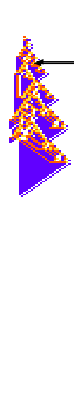
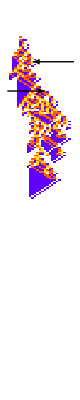
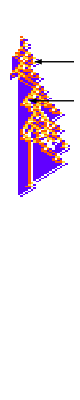

```mathematica
PlotCA/@HealCA[ru, <|{16, 206}->0|>, 3, 98 < # < 102&]
```

```mathematica
TherapySensitivityPlot[ru_, rowidx_->colspec_, steps_:200]:= Module[{ca = getca[ru, steps]},
pca = PerturbCA[{ca, ru}, rowidx->colspec];
idxs = getbodyidxs[pca];
idxfunc =  idxs[[rowidx+1;;]]&;
sensitivities = PerturbationSensitivities[{pca, ru}, (absdeltalt[ca, #2]&), ("AddValue"->1), "IndexFunction"->idxfunc];
pertreps = {rowidx, #}->Red&/@tofullform[expandrange[colspec, Length[idxs[[rowidx]]]]][[1]];
marked = ReplacePart[Join[idxs[[;;rowidx]]/. {_Integer, _Integer}->LightGray,sensitivities], pertreps];
PlotSensitivities[pca, marked]
]
```

## Micro

```mathematica
RuleTuples[k_,r_]:=RuleTuples[k,r]=Tuples[
Reverse[Range[0,k-1]],2r+1]
```

```mathematica
RuleMask[{ru_,k_,r_},lt_]:=Module[
{data,mask,canonical},
data=Union[Catenate[Map[Partition[#,2r+1,1]&,
CellularAutomaton[{ru,k,r},
CenterArray[1,2 r*(lt+4)+1],lt+2]]]];
mask=Lookup[Association[Thread[data->1]],RuleTuples[k,r],0]
]
```

```mathematica
getperts[tup_, k_]:= Tuples[Replace[ReplacePart[tup, 
Ceiling[Length[tup] / 2]->Complement[Range[0, k - 1], tup[[{Ceiling[Length[tup] / 2]}]]]],
i_Integer:> {i}, 1]]
```

```mathematica
getpertrus[i_, perts_]:= {i, #}&/@ perts
```

```mathematica
getsubs[{n_, k_, r_}]:= MapThread[#1->#2&, {Reverse[Tuples[Range[0, k - 1], 1 + 2r]],IntegerDigits[n, k, k^(2r+1)]}]
```

```mathematica
getpertedges[k_, r_]:= getpertrus[#, getperts[#, k]]&/@Tuples[Range[0, k - 1],4r+ 1]
```

```mathematica
getruparts[{arr1_, arr2_}, r_:1]:= Transpose[Partition[#, 2r+1, 1]&/@ {arr1, arr2}]
```

```mathematica
pertdiffs[{n_, k_, r_}]:= Block[{ruparts, stepped},
 ruparts =Map[getruparts[#, r]&, getpertedges[k, r], {2}];
stepped = Replace[ruparts, l_List:> Replace[l, getsubs[{n, k, r}], {4}]];
Map[Abs[#[[1]] - #[[2]]]&, stepped, {3}]]
```

```mathematica
getpertpairs[{n_, k_, r_}, active_]:= (getpertrus[#, getperts[#, k]]&/@active)
```

```mathematica
pertdiffs[{n_, k_, r_}, pertpairs_]:= Block[{ruparts, stepped},
 ruparts =Map[getruparts[#, r]&, pertpairs, {2}];
stepped = Replace[ruparts, l_List:> Replace[l, getsubs[{n, k, r}], {4}]];
Map[Abs[#[[1]] - #[[2]]]&, stepped, {3}]]
```

```mathematica
totalpertdiffs[ru_]:= Total[pertdiffs[ru], 3]
```

```mathematica
getruleloc[bits_, k_, r_] := FirstPosition[RuleTuples[k, r], bits][[1]]
```

```mathematica
plotrule[rule_, ops:OptionsPattern[{"Trim"->{None, None}, ColorRules->colorrules,Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= 
Module[{digits, n, k, r},
{n, k, r} =interpretrule[rule];
digits = IntegerDigits[n, k, k^(2r+1)];
ArrayPlot[{digits}, ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
]
```

```mathematica
plotmaskedrule[rule_, ops:OptionsPattern[{"Overlap"->False,"Trim"->{None, None}, ColorRules->withmask,Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= 
Module[{n, k, r, mult, mask, masked,digits},
{n, k, r} =interpretrule[rule];
digits = IntegerDigits[n, k, k^(2r+1)];
mult = If[OptionValue["Overlap"], -1, 100];
mask = RuleMask[rule, TestLifetime[rule, 200]]*mult;
masked = (mask/. 0:> 1) * ReplaceAll[digits, 0:> 100];
ArrayPlot[If[OptionValue["Overlap"], {masked}, {digits, mask}], ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
]
```

```mathematica
getgenelocs[{pca_, ru_}]:= Module[{n, k, r, pidxs, windows, oldwindows, newwindows, oldrulesets, newrulesets, genepairs, locs}, 
{n, k, r} = interpretrule[ru];
pidxs = Position[pca, perturb[_,_], {}];
windows = pca[[#[[1]], #[[2]]- 2r;;#[[2]]+ 2r]]&/@ pidxs;
oldwindows = # /. perturb[old_Integer, new_Integer]:> old&/@windows;
newwindows = # /. perturb[old_Integer, new_Integer]:> new&/@windows;
oldrulesets = Partition[#, 2r+1, 1]&/@ oldwindows;
newrulesets = Partition[#, 2r+1, 1]&/@ newwindows;
genepairs = MapThread[{#1, #2}&, {oldrulesets, newrulesets}, 2];
locs = Map[getruleloc[#, k, r]&, genepairs, {3}]
]
```

```mathematica
withmask =Join[colorrules, {100->GrayLevel[0.2]}];
```

```mathematica
getmidx[x1_, x2_]:= (x1 - x2)/ 2+x2
```

```mathematica
getcurves[locs_, {n_, k_, r_}, y_:2]:= Module[{digs, cols, withmid, pts, curves, styled},
digs = IntegerDigits[n, k];
cols = If[digs[[#[[1]]]] == digs[[#[[2]]]],RGBColor[0.36, 0.8300000000000001, 0], RGBColor[1., 0.63, 0.1]]&/@ Flatten[locs, 1];
withmid = Map[{#[[1]], getmidx[#[[1]], #[[2]]], #[[2]]}&, locs - 1/2, {2}];
pts = Map[{{#[[1]], y}, {#[[2]], Min[Max[(Abs[#[[3]]- #[[1]]] + 1)/2, y+3], 10]}, {#[[3]], y}} &, withmid, {2}];
curves = Flatten[Map[BezierCurve, pts, {2}], 1];
styled = MapThread[Style[#1, #2]&, {Arrow/@ curves, cols}];
Graphics[{Arrowheads[0.025],GrayLevel[0.4], styled}]
]
```

```mathematica
PerturbedRulePlot[{pca_, ru_}, ops:OptionsPattern[]]:= 
With[{allops = Merge[{"Mask"->False, ops},Last]},
If[allops["Mask"], Show[plotmaskedrule[ru],getcurves[getgenelocs[{pca, ru} ],ru, 2], Sequence@@FilterRules[Normal[allops], Options[Graphics]]], 
Show[plotrule[ru],getcurves[getgenelocs[{pca, ru}], ru, 1], Sequence@@FilterRules[Normal[allops], Options[Graphics]]]]]
```

```mathematica
activebodytups[{ca_, ru_}, tupfunc_:(4#+1&)]:= Module[{n, k, r, lt, bodytups}, 
{n, k, r} = interpretrule[ru];
lt = TestCALifeTime[ca];
bodytups = Partition[#, tupfunc[r], 1]&/@MapThread[#1[[#2[[1]] - 2r;; #2[[2]] + 2r]]&, {ca[[;;lt]], (nonzeroRange/@ca)[[;;lt]]}]]
```

```mathematica
getpertpairs[{n_, k_, r_}, active_]:= (getpertrus[#, getperts[#, k]]&/@active)
```

```mathematica
pertdiffs[{n_, k_, r_}, pertpairs_]:= Block[{ruparts, stepped, mask},
 ruparts =Map[getruparts[#, r]&, pertpairs, {2}];
stepped = Replace[ruparts, l_List:> Replace[l, getsubs[{n, k, r}], {4}]];
mask = Map[Replace[#[[1]] - #[[2]], Except[0]->1]&, stepped, {3}];
Total[mask, {3}]]
```

```mathematica
meanmicrofragility[{ca_, ru_}]:= Module[{n,k, r,counts, pd},
counts = ReverseSort[Counts[Flatten[activebodytups[{ca, ru}], 1]]];
pd = pertdiffs[ru, getpertpairs[ru, Keys[counts]]];
N@Mean[WeightedData[Mean/@ pd, Values[counts]]]
]
```

```mathematica
PerturbationSensitivityGraphs[{ca_, ru_}, size_:1]:= Module[
{counts =Rest[Counts[Sort[Flatten[activebodytups[{ca, ru}], 1]]]]*size, 
pairs, diffs, edges, cols, styled, cg, cgs, gps},
pairs = getpertpairs[ru,Keys[counts]];
diffs = pertdiffs[ru,pairs];
edges = Map[#[[1]]->#[[2]]&, pairs, {2}];
cols = Map[Replace[#, {0:>RGBColor[0, 0.77, 0],1:>RGBColor[0.88, 0.84, 0], 2:> Orange,3:> Red}]&, diffs, {2}];
styled  = 
MapThread[Style[#1,#2 ]&, {edges,cols}, 2];
cg = WeaklyConnectedGraphComponents[Flatten[styled]];
cgs = ReverseSortBy[cg, Total[counts[#]&/@EdgeList[#][[All, 1]]]&];
gps = With[{cw =Total[counts[#]&/@EdgeList[#][[All, 1]]], vws =#->counts[#]/20&/@VertexList[#]}, 
GraphPlot[#,ImageSize->cw*.75,EdgeShapeFunction->{{"FilledArrow"},(Style[Arrow[#1],
Arrowheads[counts[#2[[1]]]/200], Thickness[(counts[#2[[1]]]/(cw*5))]]&)}, 
VertexLabels->{x_/;counts[x]>=8:>Placed[ArrayPlot[{x},
Mesh->True,ImageSize->1.25counts[x], ColorRules->colorrules],Center]}]]&/@ cgs;
Multicolumn[gps, {Automatic, Floor[Length[counts]/12]}]
]
```

```mathematica
Options[PerturbationSensitivityChart] = {"NumBars"->100, "ShowSequences"->False, "TuplesFunction"->(4#+1&)};
PerturbationSensitivityChart[{ca_, ru_}, OptionsPattern[PerturbationSensitivityChart]]:= 
Module[{counts =Rest[Counts[Sort[Flatten[activebodytups[{ca, ru}, OptionValue["TuplesFunction"]], 1]]]], n, k, r, pp, pd,
withcols, labfunc},
{n, k, r} = interpretrule[ru];
pp = getpertpairs[ru,Keys[ReverseSort[counts]]];
pd = pertdiffs[ru,pp];
withcols =  MapThread[Style[#1, Blend[{RGBColor[0, 0.77, 0],RGBColor[0.88, 0.84, 0], Orange,Red},Total[#2]/((k - 1) * (2r+1))]]&, 
{Values[ReverseSort[counts]], pd}][[;;UpTo[Replace[OptionValue["NumBars"], All:> Length[pd]]]]];
labfunc = If[OptionValue["ShowSequences"], (Placed[PlotCA[Transpose@{Keys[ReverseSort[counts]][[#2[[2]]]]}, ImageSize->{20, 30}],Below]&), Automatic];
BarChart[withcols, LabelingFunction-> labfunc]]
```

```mathematica
RuleFrequencyChart[{ca_, ru_}, OptionsPattern[PerturbationSensitivityChart]]:=
Module[{counts =Counts[Flatten[activebodytups[{ca, ru}], 1]], n, k, r, pp, pd,
withcols, labfunc},
counts =Counts[Flatten[activebodytups[{ca, ru}, OptionValue["TuplesFunction"]], 1]];
{n, k, r} = interpretrule[ru];
pp = getpertpairs[ru,Keys[ReverseSort[counts]]];
pd = pertdiffs[ru,pp];
labfunc = If[OptionValue["ShowSequences"], 
(Placed[ArrayPlot[Transpose@{Keys[ReverseSort[counts]][[#2[[2]]]]}, ImageSize->{20, 20}, ColorRules->colorrules],Below]&), Automatic];
BarChart[Values[ReverseSort[counts]], LabelingFunction-> labfunc]]
```

## Adaptive Cellular Automaton

```mathematica
ClearAll@AdaptCA
```

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
getevofunc[pertfunc_, nperts_, allops_Association]:= 
Function[evoobject, Block[{nru = allops["VariationFunction"][evoobject["rule"]], nca,ncas,  ffit, nfit,nfits, nobject}, 
nca = allops["AutomatonFunction"][nru];
ffit  = allops["FitnessFunction"][nca];
If[allops["FitnessDeathValue"] ==  ffit, evoobject,
ncas = Join[{nca}, Table[pertfunc[{nca, nru}], nperts]];
nfits = allops["FitnessFunction"]/@ncas; 
nfit = allops["CombinationFunction"][nfits];
nobject = <|"rule"-> nru, "fitness"->nfit, "cas"-> ncas|>;
Merge[KeyIntersection[{evoobject, nobject}],If[allops["SelectionFunction"][evoobject["fitness"], nfit], Last, First]] 
]]]
```

```mathematica
getevofunc[pertfunc_, nperts_, allops_Association]:= 
Function[evoobject, Block[{nru = allops["VariationFunction"][evoobject["rule"]], nca,ncas,  ffit, nfit,nfits, nobject}, 
nca = allops["AutomatonFunction"][nru];
ffit  = allops["FitnessFunction"][nca];
If[allops["FitnessDeathValue"] ==  ffit, evoobject,
ncas = Join[{nca}, Table[pertfunc[{nca, nru}], nperts]];
nfits = allops["FitnessFunction"]/@ncas; 
nfit = allops["CombinationFunction"][nfits];
nobject = <|"rule"-> nru, "fitness"->nfit|>;
Merge[KeyIntersection[{evoobject, nobject}],If[allops["SelectionFunction"][evoobject["fitness"], nfit], Last, First]] 
]]]
```

```mathematica
getinitobject[initrule_, pertfunc_,nperts_, allops_Association]:= Module[{ca, pcaops, initcas, initfits, initobject},
ca = allops["AutomatonFunction"][initrule];
initcas = Join[{ca}, Table[pertfunc[{ca, initrule}], nperts]];
initfits = allops["FitnessFunction"]/@initcas; 
initobject =  <|"rule"-> initrule, "fitness"->allops["CombinationFunction"][initfits], If[allops["ReturnCAs"],"cas"-> initcas,Nothing]|>
]
```

```mathematica
Options[AdaptCA] = {"VariationFunction"->RandomRuleMutation,"AutomatonFunction"->getca, "FitnessFunction"->TestCALifeTime,
"FitnessDeathValue"->-Infinity,"Perturbation"->None,"NPerturbations"->1,"CombinationFunction"->Min, "SelectionFunction"->Function[{fit1, fit2}, fit2>=fit1], "ReturnCAs"->False, "ReturnPerturbations"->False, "PerturbationFunction"->None};
AdaptCA[initrule_List:{0, 3, 1}, iterations_:100,ops:OptionsPattern[]]:= Module[
{allops, ca, pcaops, pertfunc, initcas, initfits, initobject, nperts, evofunc, ncas, nfits, nobject},
allops = Merge[{Options[AdaptCA], ops}, Last];
nperts = If[allops["Perturbation"]===None &&allops["PerturbationFunction"] === None, 0, allops["NPerturbations"]];
pertfunc = If[allops["PerturbationFunction"]=!= None, allops["PerturbationFunction"],Replace[allops["Perturbation"], 
{None-> (#&),True-> (PerturbCA[#, pcaops]&), o_:>  (PerturbCA[#, o, pcaops]&)}]];
initobject = getinitobject[initrule, pertfunc,nperts, allops];
evofunc = getevofunc[pertfunc, nperts, allops];
NestList[evofunc, initobject, iterations]]
```

```mathematica
Options[AdaptCA] = {"VariationFunction"->RandomRuleMutation,"AutomatonFunction"->getca, "FitnessFunction"->TestCALifeTime,
"FitnessDeathValue"->-Infinity,"Perturbation"->None,"NPerturbations"->1,"CombinationFunction"->Min, "SelectionFunction"->Function[{fit1, fit2}, fit2>=fit1], "ReturnCAs"->False, "ReturnPerturbations"->False, "PerturbationFunction"->None};
AdaptCA[initrule_List:{0, 3, 1}, iterations_:100,ops:OptionsPattern[]]:= Module[
{allops, ca, pcaops, pertfunc, initcas, initfits, initobject, nperts, evofunc, ncas, nfits, nobject},
allops = Merge[{Options[AdaptCA], ops}, Last];
nperts = If[allops["Perturbation"]===None &&allops["PerturbationFunction"] === None, 0, allops["NPerturbations"]];
pertfunc = If[allops["PerturbationFunction"]=!= None, allops["PerturbationFunction"],Replace[allops["Perturbation"], 
{None-> (#&),True-> (PerturbCA[#, pcaops]&), o_:>  (PerturbCA[#, o, pcaops]&)}]];
initobject = getinitobject[initrule, pertfunc,nperts, allops];
evofunc = getevofunc[pertfunc, nperts, allops];
NestList[evofunc, initobject, iterations]]
```

```mathematica
AdaptCAFinal[initrule_List:{0, 4, 1}, iterations_:100,ops:OptionsPattern[]]:= Module[
{allops, ca, pcaops, pertfunc, initcas, initfits, initobject, nperts, evofunc, ncas, nfits, nobject},
allops = Merge[{Options[AdaptCA], ops}, Last];
nperts = If[allops["Perturbation"]===None &&allops["PerturbationFunction"] === None, 0, allops["NPerturbations"]];
pertfunc = If[allops["PerturbationFunction"]=!= None, allops["PerturbationFunction"],Replace[allops["Perturbation"], 
{None-> (#&),True-> (PerturbCA[#, pcaops]&), o_:>  (PerturbCA[#, o, pcaops]&)}]];
initobject = getinitobject[initrule, pertfunc,nperts, allops];
evofunc = getevofunc[pertfunc, nperts, allops];
Nest[evofunc, initobject, iterations]]
```

```mathematica
AdaptCA[initobject_Association, iterations_:100, ops:OptionsPattern[]]:= 
Module[{allops, evofunc, nperts, pertfunc, pcaops},
allops = Merge[{Options[AdaptCA], ops}, Last];
nperts = If[allops["Perturbation"]===None &&allops["PerturbationFunction"] === None, 0, allops["NPerturbations"]];
pcaops = Sequence@@FilterRules[Normal[allops], Options[PerturbCA]];
pertfunc = If[allops["PerturbationFunction"]=!= None, 
allops["PerturbationFunction"],Replace[allops["Perturbation"], {None-> (#&),
True-> (PerturbCA[#, pcaops]&), o_:>  (PerturbCA[#, o, pcaops]&)}]];
evofunc = getevofunc[pertfunc, nperts, allops];
NestList[evofunc, initobject, iterations]
]
```

```mathematica
AdaptCAFinal[initobject_Association, iterations_:100, ops:OptionsPattern[]]:= 
Module[{},
allops = Merge[{Options[AdaptCA], ops}, Last];
nperts = If[allops["Perturbation"]===None &&allops["PerturbationFunction"] === None, 0, allops["NPerturbations"]];
pcaops = Sequence@@FilterRules[Normal[allops], Options[PerturbCA]];
pertfunc = If[allops["PerturbationFunction"]=!= None, 
allops["PerturbationFunction"],Replace[allops["Perturbation"], {None-> (#&),
True-> (PerturbCA[#, pcaops]&), o_:>  (PerturbCA[#, o, pcaops]&)}]];
evofunc = getevofunc[pertfunc, nperts, allops];
Nest[evofunc, initobject, iterations]
]
```

```mathematica
AdaptCAWhile[initrule_List, test_,iterations_:100, ops:OptionsPattern[]]:= Module[
{allops, ca, pcaops, pertfunc, initcas, initfits, initobject, nperts, evofunc, ncas, nfits, nobject},
allops = Merge[{Options[AdaptCA], ops}, Last];nperts = If[allops["Perturbation"]===None &&allops["PerturbationFunction"] === None, 0, allops["NPerturbations"]];pertfunc = If[allops["PerturbationFunction"]=!= None, allops["PerturbationFunction"],Replace[allops["Perturbation"], {None-> (#&),True-> (PerturbCA[#, pcaops]&), o_:>  (PerturbCA[#, o, pcaops]&)}]];initobject = getinitobject[initrule, pertfunc,nperts, allops];evofunc = getevofunc[pertfunc, nperts, allops];
NestWhile[evofunc, initobject, test,1,iterations]]
```